```mathematica
(*Exercício 1*)
rShuffle[deck_]:= Riffle[deck[[;;Ceiling[Length[deck]/2]]], deck[[Ceiling[Length[deck]/2]+1;;]]]
```

```mathematica
(*Exercício 2*)
Nest[rShuffle,Range[8],3]
Nest[rShuffle,Range[52],8]
```

{1,2,3,4,5,6,7,8}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52}

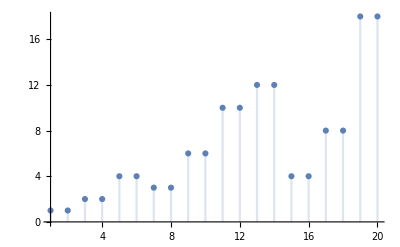

```mathematica
(*Exercício 3*)
returnIterates[list_] := NestWhile[{#[[1]]+1,rShuffle[#[[2]]]}&,{1,rShuffle[list]},#[[2]]!=list&][[1]]
ord[i_]:= returnIterates[Range[i]]
DiscretePlot[ord[i],{i,1,20}]
(*Conjetura: ord(i) = ord(i+1) para i ímpar*)
```

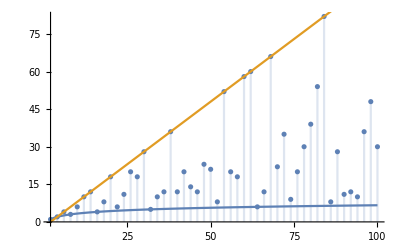

```mathematica
(*Exercício 4*)
(*Conjetura: para i par, i>2, log(i)/log(2) ≤ ord(i) ≤ i-2*)
Show[DiscretePlot[ord[i],{i,2,100,2}],Plot[{Log[x]/Log[2],x-2},{x,2,100}]]
```

```mathematica
(*Exercício 5*)
Table[If[ord[i] == Log[i]/Log[2], i,Nothing],{i,2,200,2}]
(*Claramente as potências de 2*)
```

{2,4,8,16,32,64,128}

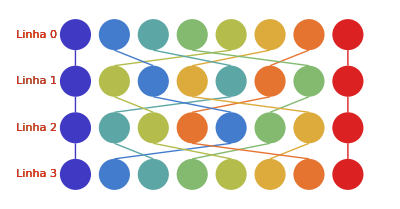

C:\Users\gaming\Desktop\theorems\ME\shuffle8.png

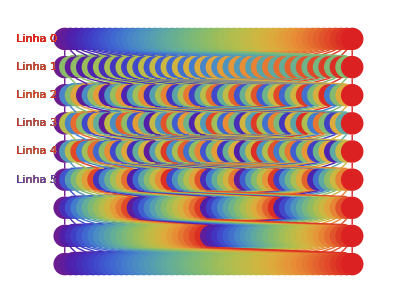

C:\Users\gaming\Desktop\theorems\ME\shuffle52.png

```mathematica
(*Exercício 6*)
(*visualização de shuffles*)
vDeltaY = .6; vDeltaX = .5; vRadius = .2;
visualizeShuffle[colors_, n_,shuffleFunction_]:=Reap[Module[{ xx=Function[i,vDeltaX (i-1)],addrow, permutation, nowcolors=colors, nextcolors=colors},
addrow = Function[{y},
Do[Sow[nowcolors[[i]]];Sow[Disk[{xx[i],-y vDeltaY},vRadius]];
Sow[Text["Linha "<>ToString[y], {-.5,-y vDeltaY}]],
{i,Length[colors]}]];
addrow[0];
Do[
permutation=rShuffle[Range[Length[colors]]];
nowcolors = Table[nowcolors[[permutation[[j]]]],{j,Length[colors]}];
Do[Sow[nowcolors[[j]]];
Sow[Line[{{xx[permutation[[j]]],(1-i)vDeltaY-vRadius},{xx[j],-i vDeltaY+vRadius}}]],
{j,Length[colors]}];
addrow[i]
,{i,n}]
]][[2,1]]//Graphics
shuffle8 =visualizeShuffle[Map[ColorData["Rainbow"], Range[8]/8],3,rShuffle]
Export[NotebookDirectory[]<>"shuffle8.png",shuffle8, ImageResolution->600]
shuffle52 = Block[{vRadius=.2, vDeltaX=.1,vDeltaY=.5},
visualizeShuffle[Map[ColorData["Rainbow"], Range[52]/52],8,rShuffle]]
Export[NotebookDirectory[]<>"shuffle52.png",shuffle52, ImageResolution->600]
```